# Optimización de la supervivencia de las colonias de insectos

Sofía Palacios Cuevas, Martín Morales Trejo,
UNAM - ENES J
Diciembre 09, 2021

1.a. A continuación graficaremos cada u(t) propuesta para describir el comportamiento de la colonia en el intervalo cerrado [0,205].

```mathematica
u1=0.5 + (0.5*Sin[(π/205)*t])
```

0.5+0.5 Sin[(π t)/205]

```mathematica
u2=(1/205)*t
```

t/205

```mathematica
u3 = 1-(1*t/205)
```

1-t/205

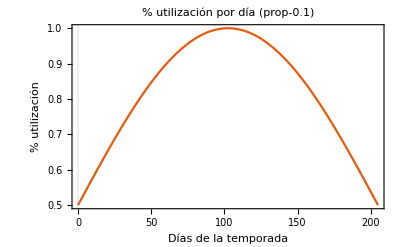

```mathematica
Plot[u1,{t,0,205},PlotTheme->"Scientific", FrameLabel->{{HoldForm[% utilización],None},{HoldForm[Días de la temporada],None}},PlotLabel->HoldForm[% utilización por día (prop-0.1)],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

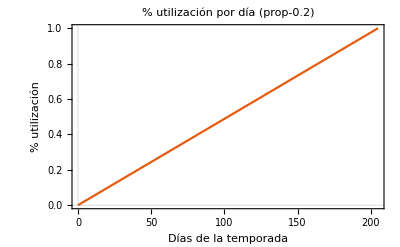

```mathematica
Plot[u2,{t,0,205},PlotTheme->"Scientific", FrameLabel->{{HoldForm[% utilización],None},{HoldForm[Días de la temporada],None}},PlotLabel->HoldForm[% utilización por día (prop-0.2)],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

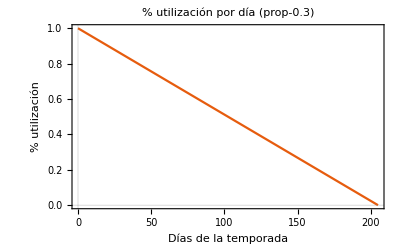

```mathematica
Plot[u3,{t,0,205},PlotTheme->"Scientific", FrameLabel->{{HoldForm[% utilización],None},{HoldForm[Días de la temporada],None}},PlotLabel->HoldForm[% utilización por día (prop-0.3)],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

1.c. Ahora calcularemos el número de insectos reina al final de la temporada Q(205)

1.d. Finalmente, graficaremos ambos Q(t) y W(t) en el intervalo de tiempo [0, 205] con las variables identificadas.

```mathematica
b=0.0013
c=1
μ= 0.022
v=0.005
T=205
R[t_]=50
```

0.0013

1

0.022

0.005

205

50

```mathematica
DSolve[(b*u1*R[t_]*W[t_])-(μ*W[t_])]
```

DSolve::argmu: DSolve called with 1 argument; 3 or more arguments are expected.

DSolve[-0.022 W[t_]+0.065 (0.5+0.5 Sin[(π t)/205]) W[t_]]

```mathematica
u4 =1- (2t/ 205)
```

1-(2 t)/205

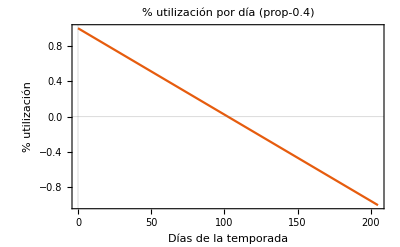

```mathematica
Plot[u4,{t,0,205},PlotTheme->"Scientific", FrameLabel->{{HoldForm[% utilización],None},{HoldForm[Días de la temporada],None}},PlotLabel->HoldForm[% utilización por día (prop-0.4)],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```